# Import J from cs_dump2

Verifying/tuning the conjugate gradient (Krylov subspace) solver.

```mathematica
SetDirectory[NotebookDirectory[]~FileNameJoin~"temp"];
$j=Import["J2.txt","Table"];
$b=1.Flatten@Rest@Import["minusFx.txt","Table"];

$js=$j//First;

$jd=($j//Rest(*extra rest: skip NNZ, can be inferred*)//Rest);
$jd=Function[{i,j,x},{i,j}+1->1.x]@@@$jd;

$jm=SparseArray[$jd,$js,0.];
Dimensions@$jm
Dimensions@$b

$sol=LeastSquares[$jm,$b,Method->"Krylov"]

$h=1.Flatten@Rest@Import["h.txt","Table"];
"maximum error versus Mathematica machine precision solution"
Max[$sol-$h]
```

{5632,1024}

{5632}

{0.,0.00236476,0.,0.0013787,0.,-0.00848717,0.,-0.0365125,0.,-0.0821185,0.,-0.0133319,0.,0.010882,0.,-1.96586×10^-6,0.,-0.0012176,0.,-0.00306305,0.,-0.013645,0.,-0.0466691,0.,-0.0485462,0.,0.0697806,0.,0.0528401,0.,-0.00100427,0.,-0.0183597,0.,-0.021814,0.,-0.0263595,0.,-0.0524885,0.,-0.00151438,0.,0.0683922,1.57813,0.10185,0.,0.0000614614,0.,-0.0603722,0.,-0.0660558,0.,-0.0587508,0.,-0.0702819,0.,-0.102106,0.,-0.0247177,0.,0.00584941,0.,-4.44212×10^-6,0.,-0.130887,0.,-0.0317134,0.,-0.112003,0.,-0.11434,0.,-0.132451,0.,-0.146221,0.,-0.129459,0.,-0.0698801,0.,-0.0120718,0.,0.00222936,0.,-0.175752,0.,-0.0808496,0.,-0.046301,0.,-0.0602593,0.,-0.00565612,0.,-0.0526899,0.,0.0410722,0.,-0.0100899,0.,0.00772059,0.,0.0460305,0.,-0.0186511,0.,0.00614118,0.,0.0410081,0.,-0.0120341,0.,0.0556852,0.,0.050659,0.,0.0152224,0.,0.021695,0.,0.00540451,0.,-0.0122669,0.,0.0539687,0.,0.0478931,0.,-0.00208858,0.,-0.00628066,0.,-0.0302929,0.,-0.0982326,0.,0.0340472,0.,0.0568119,0.,0.060873,0.,0.0391785,0.,-0.0144069,0.,-0.0212562,0.,-0.0462376,0.,0.0764444,0.,0.104128,0.,0.126316,0.,0.145546,0.,0.0593446,0.,-0.0572924,0.,-0.0699478,0.,-0.0802437,0.,-0.137676,0.,0.10024,0.,0.12428,1.65394,0.150723,0.,0.0852571,0.,-0.15684,0.,0.0215876,0.,-0.159501,0.,-0.182866,0.,-0.155488,0.,0.0359036,0.,0.0618553,-0.0796677,0.135572,0.,0.133245,0.,0.031984,0.,-0.172997,0.,-0.0782251,0.,-0.117113,0.,-0.0996259,0.,-0.0777284,0.,-0.0215629,0.,0.0108522,0.,0.0277393,0.,-0.137472,0.,0.00311029,0.,0.0252879,0.,0.00110231,0.,0.00504276,0.,0.00416454,0.0321337,0.049289,0.0293471,0.0415421,0.,0.0133868,0.0114417,0.0464783,0.0113919,0.0223513,0.0121032,0.0452206,0.0147385,0.0317372,0.0187526,-0.0344811,0.0246923,0.0589328,0.,0.00959824,0.,0.0186007,0.00892217,0.0219718,0.00885537,-0.00234998,0.00999383,-0.0267593,0.,0.0396786,0.591054,0.0592404,0.,-0.0244822,0.,-0.0349414,0.,-0.0756402,0.,-0.187822,0.,0.111106,0.0208222,0.0846798,0.0141275,0.11372,0.,0.0370703,0.,-0.0540737,0.,-0.0692364,0.,-0.108502,0.,-0.226337,0.0227379,0.16788,0.0177964,0.140848,0.00771242,0.141046,-0.114418,0.111503,0.,-0.132615,0.,-0.161203,0.,-0.176964,0.,-0.262255,-0.0616249,0.161781,-0.00804679,0.133268,0.0972305,0.154748,-1.50947,0.149789,0.,-0.300009,0.,0.0959975,0.,-0.071172,0.,-0.299937,0.,-0.110363,0.,0.00189563,-0.00746059,0.0799866,-0.720294,0.209716,0.0544785,0.153799,0.062398,0.0707944,0.,-0.140243,0.,-0.0436497,0.,-0.0504038,0.,-0.0453336,0.00645655,-0.0129712,-0.263812,0.104106,0.0418018,0.0572882,0.0353978,0.073729,0.0268457,-0.0834945,0.0141719,0.0537327,0.0129639,0.0181275,0.0126928,-0.0123048,0.0132563,-0.00679784,0.0143374,0.0508848,0.0321337,0.0418098,0.0293471,0.0330244,0.020912,0.00471099,0.0114417,0.0337792,0.0113919,0.00404692,0.0121032,0.0234695,0.0147385,0.00911472,0.0187526,-0.00915682,0.0246923,0.0546,0.0243957,-0.0441429,0.0119699,-0.0365071,0.00892217,0.0125323,0.00885537,-0.0226968,0.00999383,-0.0514258,0.016093,0.0172202,0.0264118,0.0206269,0.,-0.0888789,0.,-0.108359,0.,-0.166849,0.,-0.322015,0.0310631,0.103414,0.0208222,0.0942216,0.0141275,0.108197,0.00646232,0.0280357,0.,-0.144945,0.,-0.169951,0.,-0.224772,0.0227379,-0.384181,0.0227379,0.135061,0.0177964,0.137581,0.00771242,0.129013,-0.00797001,0.0963548,0.,-0.213447,0.,-0.257264,0.,-0.327449,-0.0616249,-0.385267,-0.0616249,0.199241,-0.00804679,0.108052,-0.00521713,0.0916056,-1.26159,0.204403,0.0544785,-0.295163,0.0426634,0.166573,0.019495,-0.0295128,0.,-0.266903,-0.0245266,-0.147797,0.000218313,-0.0545543,-0.00746059,0.0296338,-1.02361,0.194683,0.0544785,0.143534,0.062398,0.0296013,0.0359638,-0.128911,0.0171568,-0.0422386,0.0151833,-0.0608184,0.0117627,-0.110695,0.00645655,-0.0194498,-0.500618,0.14483,0.0501125,0.1009,0.0423668,0.0746152,0.0268457,-0.0417062,0.0170543,0.0355072,0.0145207,-0.00480762,0.0132799,0.0132122,0.0117954,-0.0271356,0.0100257,0.0359098,0.0347326,0.0809546,0.0279725,0.0706124,0.0208292,0.0358566,0.013847,0.0618939,0.0124155,-0.0160044,0.0122015,0.00591579,0.0134072,0.0482428,0.0145698,0.0389352,0.0246774,0.0468858,0.0192737,0.0435313,0.0146167,-0.0493779,0.0102534,0.00140747,0.00923786,-0.0265674,0.00980044,-0.0569565,0.0144687,0.0236895,0.0219378,0.0448808,0.,-0.0865763,0.,-0.109368,0.,-0.180711,0.0530136,-0.315828,0.0530136,0.164989,0.0298233,0.111479,0.0177791,0.123089,0.0149063,0.139325,0.,-0.0674215,0.,-0.0951571,0.,-0.163662,0.103585,-0.353981,0.103585,0.0959456,0.0365569,0.16852,0.0139139,0.166109,-0.00336812,0.14536,0.,-0.154872,0.0230716,-0.198698,0.019495,-0.287844,0.,-0.358658,0.0222381,-0.480363,0.0305597,0.0919981,0.00677967,0.101631,-0.0170827,0.182173,0.0188694,-0.242426,0.0230716,0.239024,0.019495,-0.0156298,0.0147989,-0.170976,0.014631,-0.0966742,0.017148,-0.105471,0.0113364,-0.00160926,0.0200914,0.104081,0.0481481,0.21392,0.0408132,0.199851,0.0234179,-0.0347558,0.0172531,-0.017183,0.0158312,-0.0823305,0.0154828,-0.134011,0.0149101,-0.0242202,0.0374543,0.0604789,0.0456328,0.121854,0.0381104,0.0791186,0.0266492,-0.0635891,0.0179252,0.0118996,0.015635,-0.0228667,0.0145701,0.00162965,0.0142888,0.0134841,0.0166849,0.0322637,0.0347326,0.09334,0.0326702,0.0678268,0.0205742,0.0241952,0.0158409,0.0537413,0.0140228,-0.0171938,0.0133843,0.016624,0.0138443,0.0728372,0.0156459,0.0713707,0.0246774,0.0528165,0.0167726,0.0428326,0.0144568,-0.0572973,0.0125813,0.00395604,0.00923786,-0.0227763,0.00980044,-0.0350146,0.,0.0735226,0.278001,0.117439,0.,-0.0527908,0.,-0.072781,0.,-0.141844,0.0361251,-0.264762,0.0361251,0.24365,0.0326938,0.223188,0.0177791,0.227808,0.0149063,0.176523,-0.0300815,-0.0439611,-0.0233615,-0.0708688,-0.0196643,-0.132446,-0.0192994,-0.279855,-0.324034,0.289733,0.0365569,0.276726,0.0135569,0.255805,-0.462746,0.201542,-0.0243814,-0.0898038,-0.0100564,-0.185627,-0.00450609,-0.280879,-0.00678745,-0.281131,-0.0163052,-0.393438,0.0226994,0.217763,-0.00121339,0.126491,-0.00846875,0.176414,-0.0141557,-0.116648,0.00767621,0.261194,0.0127001,0.0275072,0.0080397,-0.124742,0.0127241,-0.076573,0.0146067,-0.0664956,0.0238681,0.0210692,0.0417411,0.092307,0.0167298,0.271897,0.0215866,0.231629,0.0175008,0.011887,0.0138602,-0.0118478,0.0141666,0.0380561,0.0150467,-0.0496553,0.0149101,0.00929936,0.0396477,0.0346402,0.,0.20178,0.0381104,0.130843,0.022124,0.0189321,0.015791,0.0537435,0.015635,0.0828776,0.0145701,0.0727352,0.0142888,0.0863694,0.0166849,0.0587882,0.,0.200637,0.,0.152938,0.,0.0473063,0.,0.137858,0.,0.130824,0.,0.129103,0.,0.186642,0.,0.193048,0.,0.134096,-3259.82,0.116853,0.0144568,0.0179417,0.,0.0895911,0.,0.0747506,0.,0.0733163,0.,0.184853,0.,0.197658,-0.0207949,-0.0469627,-0.0162769,-0.0645685,-0.0132096,-0.128609,-0.0128476,-0.235639,0.0361251,0.248876,0.,0.370893,0.,0.388048,0.,0.285301,-0.0300815,-0.0396894,-0.0233615,-0.0688893,-0.0196643,-0.127117,-0.0192994,-0.253494,-0.295702,0.292892,0.,0.428009,0.,0.393271,-7.76575,0.325514,-0.0344166,-0.0763805,-0.0278928,-0.181025,-0.0234231,-0.286109,-0.022691,-0.26357,-0.0461582,-0.278699,-1.51719,0.395629,0.,0.294066,-1.55427,0.36572,-0.0339134,-0.0471153,-0.0177227,0.350026,-0.00485878,0.0594842,-0.00556019,-0.0831512,-0.0124968,-0.00554327,0.0146067,0.0483106,0.,0.197391,-1.00135,0.243478,-0.0339134,0.455388,0.,0.403577,0.0175008,0.121492,0.00426838,0.190671,0.,0.222449,0.,0.208382,0.,0.27717,0.,0.214557,-0.826351,0.550138,0.,0.400622,0.,0.30332,0.,0.361135,0.,0.36659,0.,0.376202,-0.982612,0.439047,0.,0.312104,-0.836944,0.609212,-0.905899,0.501779,0.,0.356568,-0.982578,0.48578,-0.975297,0.508468,-0.980471,0.521374,-0.918492,0.5662,-0.830838,0.470714,-0.565565,0.584264,-0.829289,0.433586,0.,0.288225,-0.748615,0.430862,-0.709024,0.449862,-0.702012,0.508822,-0.6773,0.50682,-0.577447,0.499763,-0.0116239,-0.0476193,-0.00912231,-0.0553491,-0.00695704,-0.108945,-0.00643098,-0.184468,-0.00643098,0.340607,-0.95572,0.840221,-0.820431,0.935516,-0.631382,0.76215,-0.0217751,-0.0320557,-0.0177239,-0.0629332,-0.0127195,-0.109705,-0.012391,-0.205638,-0.0122184,0.325388,-1.01984,0.894823,-0.920282,0.960196,-0.843262,0.858645,-0.0325707,-0.0519272,-0.0305213,-0.202534,-0.0210933,0.0970663,-0.0176647,-0.222418,-0.031425,-0.0731274,-0.897183,0.745694,-0.928163,0.838485,-0.751504,0.782609,-0.033223,0.102489,-1.0212,0.74526,0.,0.187328,-0.0114934,0.0718877,0.,0.142634,0.,0.289994,-0.946343,0.701787,1.21659,0.406487,-0.995124,0.975998,-0.903968,0.93542,0.,0.363371,-1.24159,0.694695,-1.159,0.785694,-1.20087,0.807141,-0.95599,0.902553,-0.724253,0.690615,0.,-0.762564,-0.97694,1.10128,-1.12349,0.937906,-1.00903,1.0467,-1.00771,1.08088,-1.00007,1.11108,0.,-0.858134,-0.791678,0.902296,0.,-0.640246,0.,-0.797699,-0.968606,1.0958,0.,-0.776696,0.,-0.71642,0.,-0.691682,0.,-0.705864,0.,-0.932328,0.,-0.538101,0.,-0.935508,-0.758037,0.968428,0.,-0.624763,0.,-0.53227,0.,-0.507653,0.,-0.498109,0.,-0.466341}

maximum error versus Mathematica machine precision solution

10.5801

## minmax

```mathematica
MinMax@$jm
MinMax@$b
MinMax@$sol
```

{-421460.,25893.9}

{-6.44987,7.69991}

{-3259.82,1.65394}

## j spectrum

1330

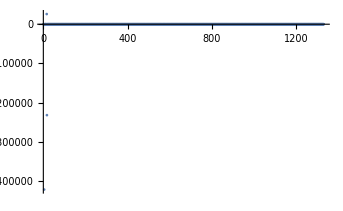

```mathematica
$fjm=DeleteDuplicates@Flatten@$jm;
$fjm//Length
ListPlot[$fjm,PlotRange->Full]
```

```mathematica
$sol2=LeastSquares[SetPrecision[$jm,30],SetPrecision[$b,30],Method->"Krylov"];
"maximum error versus Mathematica high precision solution"
Max[$sol2-SetPrecision[$h,30]]
```